```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g=Flatten[Import["NoOffset/C/best.gen.dat"]];
```

```mathematica
sw = Import["NoOffset/C/sensorweights.dat"];
```

```mathematica
iw = Import["NoOffset/C/interweights.dat"];
```

```mathematica
mw = Import["NoOffset/C/motorweights.dat"];
```

```mathematica
ArrayPlot[sw,ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->250]
Export["sw.eps",%]
```

-Graphics-

sw.eps

```mathematica
ArrayPlot[iw,ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->250]
Export["iw.eps",%]
```

-Graphics-

iw.eps

```mathematica
ArrayPlot[Transpose[mw],ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->250]
Export["mw.eps",%]
```

-Graphics-

mw.eps

```mathematica
width = 6;
```

```mathematica
neuronpos = {{-width,0},{-width/2,0},{0,0},{width/2,0},{width,0}};
```

```mathematica
c15={{-width,0},{-(3 width)/4,width/2},{-width/2,0}};
c25={{-width,0},{(3 width)/4,width/2},{0,0}};
c35={{-width,0},{(3 width)/4,width/2},{width/2,0}};c45={{-width,0},{(3 width)/4,width/2},{width,0}};
```

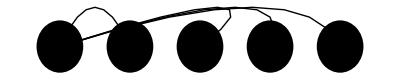

```mathematica
Graphics[
{
Disk[neuronpos[[1]]],
Disk[neuronpos[[2]]],
Disk[neuronpos[[3]]],
Disk[neuronpos[[4]]],
Disk[neuronpos[[5]]],
BezierCurve[c15],
BezierCurve[c25],
BezierCurve[c35],
BezierCurve[c45]
}
]
```